## Integration Test

Define a set of functions to be integrated

Define a set of intervals on which `NIntegrate` should be performed

Measure the timing performance of both version of Mathematica

```mathematica
myFunction[k_,a_]:=Sum[i*a*Sin[#]^i,{i,k,0,-1}]&[x];
functionGrupx[n_,a_]:=Table[myFunction[k,a][x],{k,1,n}];
t25=Table[i,{i,1,25,1}];
t55=Table[i,{i,1,50,1}];
t75=Table[i,{i,1,75,1}];
t[ops_]:=Table[i,{i,1,ops,1}];
```

### Example with t

```mathematica
t[5]
t[12]
```

{1,2,3,4,5}

{1,2,3,4,5,6,7,8,9,10,11,12}

### Create threaded operation

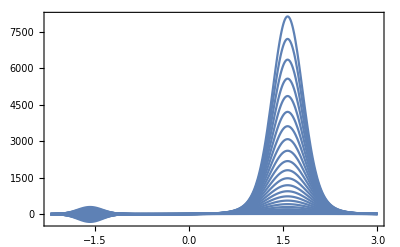

```mathematica
(*(list of functions)*)
thop[lister_]:=MapThread[myFunction,{lister,lister}];
Plot[thop[t25],{x,-2.2,3},PlotRange->Full,Frame->True,Axes->False]
```

### Example with thop (list of functions)

```mathematica
thop[t[0]]
thop[t[1]]
thop[t[3]]
```

{}

{Sin[x]}

{Sin[x],2 Sin[x]+4 Sin[x]^2,3 Sin[x]+6 Sin[x]^2+9 Sin[x]^3}

```mathematica
functionGrupx[10,1]
```

{Sin[x][x],(Sin[x]+2 Sin[x]^2)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3+4 Sin[x]^4)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3+4 Sin[x]^4+5 Sin[x]^5)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3+4 Sin[x]^4+5 Sin[x]^5+6 Sin[x]^6)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3+4 Sin[x]^4+5 Sin[x]^5+6 Sin[x]^6+7 Sin[x]^7)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3+4 Sin[x]^4+5 Sin[x]^5+6 Sin[x]^6+7 Sin[x]^7+8 Sin[x]^8)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3+4 Sin[x]^4+5 Sin[x]^5+6 Sin[x]^6+7 Sin[x]^7+8 Sin[x]^8+9 Sin[x]^9)[x],(Sin[x]+2 Sin[x]^2+3 Sin[x]^3+4 Sin[x]^4+5 Sin[x]^5+6 Sin[x]^6+7 Sin[x]^7+8 Sin[x]^8+9 Sin[x]^9+10 Sin[x]^10)[x]}

```mathematica
Do[Print[AbsoluteTiming[functionGrupx[100,1]][[1]]],{i,1,10,1}]
```

0.006026

0.005863

0.005939

0.006208

0.005677

0.00528

0.006213

0.005304

0.0067

0.005139

```mathematica
Do[Print[AbsoluteTiming[thop[t[125]]][[1]]],{i,1,10,1}]
```

0.009382

0.009699

0.009982

0.009859

0.0094

0.009742

0.008631

0.008274

0.009056

0.00889

```mathematica
thop[t[2]]
```

{Sin[x],2 Sin[x]+4 Sin[x]^2}

```mathematica
numint[function_,interval_]:=NIntegrate[function,{x,interval[[1]],interval[[2]]}];
```

```mathematica
batchintegrater[functions_,intervals_]:=Table[numint[functions[[i]],intervals[[i]]],{i,1,Length[functions]}];
```

```mathematica
intervalmaker[n_]:=Table[{-π,π/6},{i,1,n}];
```

```mathematica
intervalmaker[7]
```

{{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6}}

```mathematica
timer[intgsize_]:=AbsoluteTiming[pp=batchintegrater[thop[t[intgsize]],intervalmaker[intgsize]]];
```

```mathematica
timer[3]
```

{0.034872,{-1.86603,2.73231,-7.74721}}

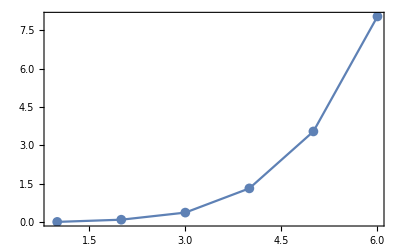

{0.000014,0.085822,0.363848,1.31162,3.53931,8.03881}

```mathematica
timetable=Table[timer[i][[1]],{i,0,50,10}];
ListPlot[timetable,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,PlotRange->Full]
Print[timetable]
```

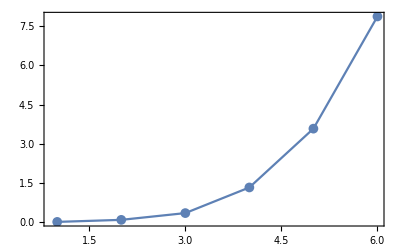

{0.00002,0.078281,0.337583,1.32091,3.5765,7.87956}

```mathematica
timetable=Table[timer[i][[1]],{i,0,50,10}];
ListPlot[timetable,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,PlotRange->Full]
Print[timetable]
```